# FAQ : Constructing Rulesets for a Specific Goal - Generating a n-Dimensional Network

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

Note:  The following code lines may be copied into a notebook with SSS code and executed, experimented with.

We now have tests of fair reliability to test the dimensionality of a sessie and its causal network.  Why test the sessie?  Because to do so is easier, faster, and requires fewer steps in the evolution before testing can occur.  Normal sessie generation (using SSS[…] or SSSInitialize and SSSEvolve) calls the function SSSSingleStep, which tests for Dead or Repeating cases at each step, but also sets $SSSVerdict equal to Pseudorepeating if there's a good chance that the network can be identified.  The function IdentifyPseudorepeating currently performs 4 tests on the sessie and 2 on the network, attempting to identify them as having some integer dimension, or exponential behavior.

But no cases of integer dimension greater than 2 had been found by running the enumeration, and no cases of integer dimension greater than 3 had been found at all, so an effort to construct such cases by handcrafting rulesets seemed promising.  This attempt was completely successful, and we now have an algorithm for constructing rulesets for sessies of any integer dimension!

The method is based on adapting a simple 1-d band network, generated by

(* for Colton, delete later! Use F1 for Help, etc. *)

```mathematica
Options[SSS]
```

{Mode→Loud,EarlyReturn→False,Mode→Silent,HighlightMethod→True,RulePlacement→Bottom,Mesh→True,NetSize→{Automatic,400},SSSSize→{Automatic,300},IconSize→{Automatic,20},ImageSize→Automatic,NetMethod→GraphPlot,Max→∞,SSSMax→Automatic,NetMax→Automatic,Min→1,SSSMin→Automatic,NetMin→Automatic,AlignmentPoint→Center,AnnotationRules→{},AspectRatio→Automatic,AutomaticImageSize→False,Axes→False,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},Boxed→False,BoxRatios→Automatic,BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→False,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DirectedEdges→Automatic,DirectedEdges→False,EdgeCapacity→Automatic,EdgeCost→Automatic,EdgeLabels→None,EdgeLabelStyle→Automatic,EdgeShapeFunction→Automatic,EdgeStyle→Automatic,EdgeWeight→Automatic,Editable→False,Epilog→{},FaceGrids→None,FaceGridsStyle→{},FormatType→TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→None,FrameTicksStyle→{},GraphHighlight→{},GraphHighlightStyle→Automatic,GraphLayout→Automatic,GraphRoot→Automatic,GraphStyle→Automatic,GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LayerSizeFunction→(1&),Lighting→Automatic,Method→Automatic,MultiedgeStyle→Automatic,PackingMethod→Automatic,PerformanceGoal→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme→Automatic,PreserveImageOptions→Automatic,Prolog→{},Properties→{},RotateLabel→True,RotationAction→Fit,SelfLoopStyle→Automatic,SphericalRegion→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→Automatic,VertexCapacity→Automatic,VertexCoordinates→Automatic,VertexLabels→None,VertexLabelStyle→Automatic,VertexShape→Automatic,VertexShapeFunction→Automatic,VertexSize→Automatic,VertexStyle→Automatic,VertexWeight→Automatic,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},DisplayFunction:>$DisplayFunction}




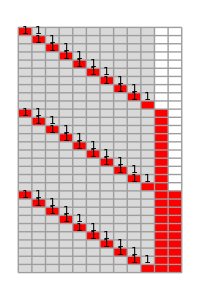
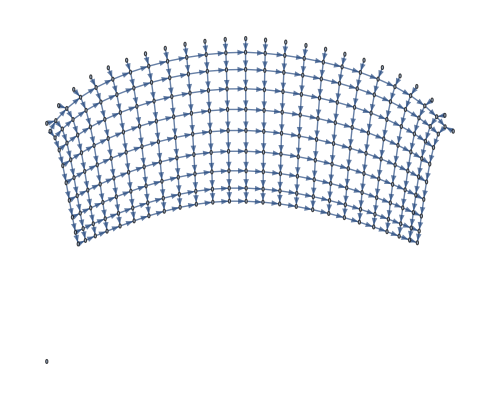
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
SSS[{"BA" -> "AB", "" -> "B"}, "BAAAAAAAAA", 250, SSSMax -> 30,  SSSSize -> {200, 300}, NetSize -> {500, 400}, VertexLabels -> None, RulePlacement -> Left]
```

The first rule swaps B & A (red and gray), and its repeated application forms the diagonal stroke, moving the B (red) all the way to the right.  A simple tweak makes each diagonal stroke longer (by 1) than the previous one, creating a 2-d network:

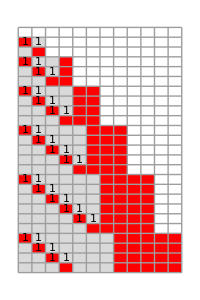
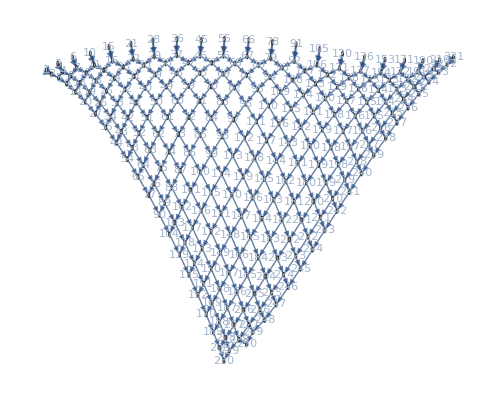
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[{"BA"->"AB",""->"BA"},"",250,SSSMax->25,SSSSize->{200,300},NetSize->{500,400},VertexLabeling->False,ShowRule->Left]
```

To make a higher-dimensional network, each diagonal stroke must be an increasing number greater than the previous one rather than a constant number greater.  Several ideas were tried, but most created exponential growth or other 2-d networks.  Eventual success:  the idea is to use a 3rd color as a marker/counter, a signal to insert an extra A (gray), lengthening the diagonal stroke, and then gradually increase the number of markers:

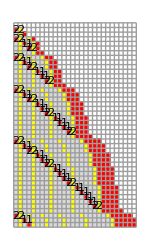
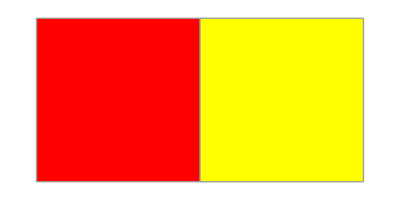
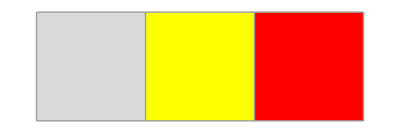
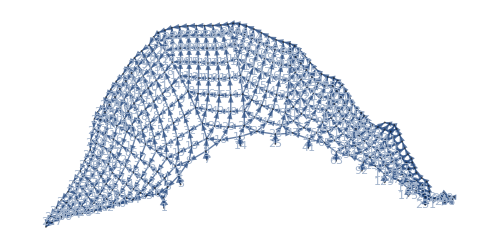
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[{"BA"->"AB","BC"->"ACB",""->"BC"},"",400,SSSMax->44,SSSSize->{150,250},NetSize->{500,250},VertexLabeling->Tooltip,ShowRule->Left]
```

This network gets too big to fit in the plane, but spiraling upwards allows it to fit in a (3-d) cone. [Note: build this visualization!] The yellows (C) are the markers, and each diagonal stroke starts by adding a C as well.  As the stroke crosses each marker, an extra gray (A) is inserted, so after the stroke that crosses 4 markers comes the stroke that crosses 5 markers, etc.  Again, the first rule makes the diagonal stroke.  The second allows the diagonal stroke to pass the yellow markers, adding in an extra gray each time.  The third rule starts a new diagonal (red) stroke and adds an extra (yellow) marker.

Here is a 3-D representation of the same network, showing that it fits in an expanding cone, but wouldn't fit in a plane:

***This is not working***

```mathematica
SSS[{"BA"->"AB","BC"->"ACB","A"->"ACB"},"A",1100,SSSMax -> 44, SSSSize ->{150,250},NetSize->{800,600},ShowRule-> Left, NetMethod-> {NoSSS,GraphPlot3D},VertexLabeling->False,BoxRatios->{.8,1,1},Boxed->False,ViewPoint->{Right} ]
```

-Graphics3D-

Now the method of extension becomes obvious:  adding one extra rule and one extra color for a nested marker gives a 4-d network:

-Graphics-

Crossing a green marker is the signal to insert a insert a gray, while crossing a yellow marker inserts both a gray and an extra green marker, so on each stroke the number of yellow markers increases by 1, and the number of green markers between any pair of yellow markers increases by one.  [Possible area for student research: tweak these rules, can a lower-weight ruleset be found? Is the extra gray square needed in the 2nd & 3rd rules?]

Similarly, 5- and 6-d networks can be generated from these rulesets:

{"BA" -> "AB", "BE" -> "AEB", "BD" -> "AEDB", "BC" -> "ADCB", "" -> "BC"}
-Graphics-

This can be extended indefinitely, nesting as many markers as needed for the desired dimension.  It is interesting that this algorithm requires n rules using n colors to generate a n-dimensional sessie network!

Question:  Can the rules be simplified/shortened while still giving this behavior?  [Student research idea!]

Answer:  Maybe!  Each of the "marker" rules shown allows the red diagonal to cross the ~vertical marker stripe:  swap the red & the marker color, and add an extra gray or marker of another color.  But I wasn't getting quite the desired behavior until I added both gray and the nested marker.  For example, Red+Green -> Gray+Cyan+Green+Red:  swap the Red & Green, creating an extra Cyan marker and inserting an extra Gray.  Why?  It seems as if this extra Gray shouldn't be needed, reducing the right-hand side lengths to a maximum of 2.  More experimentation needed.

Question:  Do all n-dimensional sessie networks have n (or more) rules in their rulesets?

Answer: Unknown.  Perhaps the enumeration will turn up a counterexample!  Or perhaps further thought can allow intelligent construction of a ruleset that uses fewer rules while still resulting in this nested behavior that creates higher-dimensional networks.  Maybe one rule can result in different behavior in different circumstances, allowing the different markers to all be handled by one rule?

Question:  Do all n-dimensional sessie networks have n (or more) colors / letters in their rulesets?

Answer: No.  It is possible to generate a network of any dimension in a way modeled on the above method, but using only two colors / symbols.  (Thanks to Charles Sarr for this idea.)

Example:

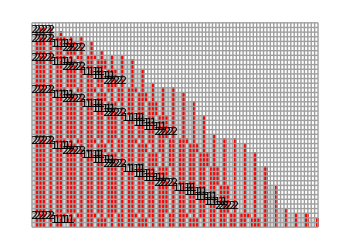
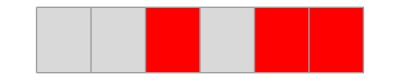
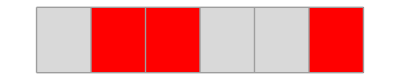
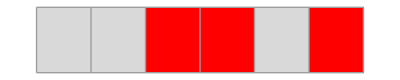
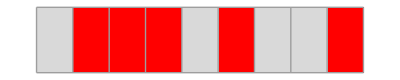
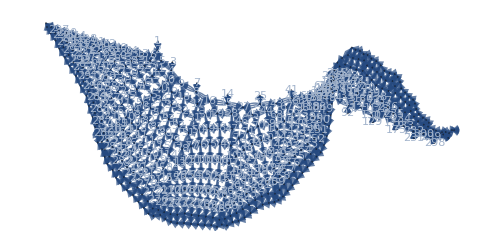
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[{"AABABB"->"ABBAAB","AABBAB"->"ABBBABAAB",""->"AABBAB"},"",500,SSSMax->44,SSSSize->{350,250},NetSize->{500,250},VertexLabeling->Tooltip,ShowRule->Left]
```

Here each color/letter in the 3-d example above was “encoded” in a binary string of gray & red (or A & B)

-Graphics-

B (Red)      -> AAB (Gray,Gray,Red) 
A (Gray)    -> ABB (Gray,Gray,Red)
C (Yellow) -> BAB (Red,Gray,Red)

Any similar encoding should work.  (We added the extra Red at the end of the code to prevent confusion where adjoining codes were misinterpreted.  There may be a better way to do this in an unambiguous way, providing a stop indicator that cannot be misread for something else, for example.)  Any number of colors can be coded using a long enough series of bits, so only 2 colors are needed to create networks of any integer dimension!

FAQ Sessie Intro, 2024.11.21, Kenneth Caviness and Colton Edelbach